# ModWheel

This notebook demonstrates the “ModWheel” code of the 4-voice Midi2CV PIC project.
Copyright © Terje B. 2006-2012

TODO: Add running data logging to file, for later import/graphing in Octave.
See: http://stackoverflow.com/questions/5286640/file-input-output-in-mathematica

```mathematica
frequency=1; notenumber := 0; modulationvalue := 63; start:=-Pi*2; incinterval:=True;
```

```mathematica
GenerateModWheelCurve[pfrequency_, pstart_, pincinterval_, pnotenumber_, pmodulationvalue_] :=
Module[{},
interval = 0.03;
curvePos=pstart;
maxModulationValue = 128; (* MAX_MIDI_NOTE + 1 *)
maxModulationRange = 12.0 / 2;
maxElements=(Ceiling[(Pi-(Pi*-1))/interval]*pfrequency)+(pfrequency-1);
counter = 0;
curveData = ConstantArray[0, maxElements];

For[counter=1, counter <= maxElements, counter++,
(
curveData[[counter]]=(Sin[curvePos] / (maxModulationValue / pmodulationvalue)*maxModulationRange)+pnotenumber;

If[pincinterval == True, interval=interval+(pfrequency/25000.0)]; (*curveInterval;*)
curvePos = curvePos + interval
)
];
{curveData, maxElements}
]
```

Test the module:

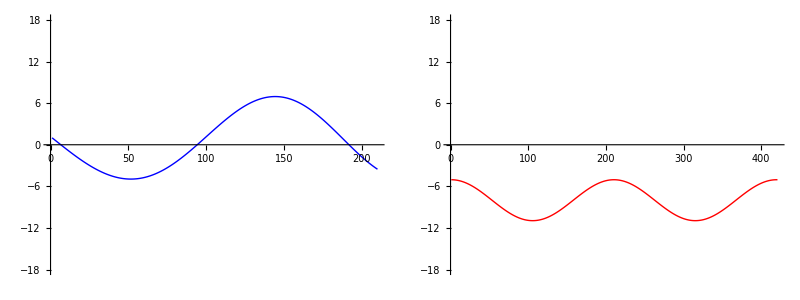

```mathematica
OpenFile[]:=
Module[{},
strOut=OpenWrite["C:\\coding\\Mathematics\\Mathematica_ModWheel.txt"];
strOut (* Return file handle for use in Manipulate block *)
];

{curveData1, maxElements1} = GenerateModWheelCurve[1, -Pi, True, 1, 127];
{curveData2, maxElements2} = GenerateModWheelCurve[2, Pi/2, False, -8, 63];
Length[curveData1];
(* Write data to file *)
strOut = OpenFile[];
Write[strOut,curveData];
Close[strOut];

g1 = Show[ListLinePlot[curveData1,  PlotStyle->Blue, PlotRange->{Automatic, {-18, 18}}], ImageSize->Scaled[.60]];
g2 = Show[ListLinePlot[curveData2,  PlotStyle->Red, PlotRange->{Automatic, {-18, 18}}], ImageSize->Scaled[.60]];
Grid[{{g1, g2}}, ItemSize->{{34, 34}}, Frame->All, FrameStyle->LightGray]
```

Animate and control the module we’ve created with the Manipulate command:

```mathematica
(*strOut = OpenFile[];*) (* Open data file for output *)
mresult = Manipulate[
{curveData,  maxElements} = GenerateModWheelCurve[frequency, start, incinterval, notenumber, modulationvalue];
(*Write[strOut,curveData];*)
g = Show[ListLinePlot[curveData,  PlotStyle->Red, PlotRange->{Automatic, {notenumber - 6, notenumber + 6}},
ImageSize->Scaled[.98]],AxesLabel->{None, "Pitch"}, Axes->{False, True},AspectRatio->.25,
GridLines->{None, {notenumber-6, notenumber, notenumber+6}}, GridLinesStyle->LightGray];
Grid[{{g}}, ItemSize->{{65, 20}}, Frame->None],
(* NOTE: 2nd cell in Grid is not shown {use: g, g}, but ItemSize is set for it (20) *)
 {{notenumber, 0, "Note Number"}, -11, 11, 1, Appearance->{"Labeled", "Open"}},
{{modulationvalue, 63, "Modulation Value"}, 1, 127, 1, Appearance->{"Labeled", "Open"}},
{{frequency, 1, "Frequency"}, 1, 6, 1, Appearance->"Labeled"},
{{start,-Pi*2, "Start point"}, -Pi*2, Pi*2, Appearance->"Labeled"},
 {{incinterval, True, "Increase Interval"}, {True, False} },
SaveDefinitions->True 
]
```

```mathematica
(* Close[strOut]; *)
```

```mathematica
(* Export["C:\coding\Mathematics\ModWheel.avi",mresult] *)
```